#### Sezione F:

#### in questa Brutta sezione F mi sembra adeguato dimostrare il teorema di Sharkovskiy (Шарко́вський) nel caso n=3 facendo riferimento (come esempio specifico) alla mappa logistica n.b. la dimostrazione è rubata a wikipedia. segue la dimostrazione completa del teorema senza riferimenti specifici alla mappa logistica in quanto molto teorica

Th: sia · → · un ordine totale definito su ℕ nel seguente modo
3 →  5 →  7 →  9 →  11 →  ...      
→  3×2 →  5×2 →  7×2 → ...     
→ 3×2^2 →  5×2^2→  7×2^2→ ... 
→  3×2^n →  5×2^n→  7×2^n→ ...   
... →2^3 →  2^2 →  2 → 1
quest’ordine ha come supremo 3, come infimo 1

Il teorema di Sharkovskiy afferma che, data f:I→I una mappa continua, se f ha un punto periodico primitivo di periodo m→n allora possiede anche un punto periodico di periodo n

vogliamo dimostrare che, se esiste un’orbita di periodo 3 allora esistono orbite di ogni periodo
indi che esistono a,b,c ∈ ℝ t.c. f:a↦b↦c↦a

si utilizzano i seguenti fatti, data una funzione f continua

· teorema del punto fisso di Brouwer, ossia I⊆f(I) ⇒ f ha un p. fisso in I
· V ⊆ f(U) ⇒ ∃ U_0⊆U : V = f(U_0)

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ# (1-#)&,x,n]]
```

CompiledFunction[…]

```mathematica
D[f[μ,x],x]
```

(1-x) μ-x μ

(1 - x) μ - x μ  = μ(1-2x)= 0 ⇔ x=1/2 supponendo μ≠0

```mathematica
f[μ,1/2](*è il massimo*)
```

μ/4

f_μ:ℝ→[-∞,μ/4] ⊂ ℝ ergo valgono le ipotesi di cui sopra.

la mappa f_μ possiede un’orbita 3-periodica in una finestra regolare per μ>μ_∞ abbiamo trovato nei punti precedenti un tale μ (che chiameremo μ_p3 d’ora in avanti) e vale ≈3.8281, in realtà la mappa con orbite di periodo 3 vale circa da 3.828 a 3.841 quindi per comodità prendiamo μ_p3=3.835
ridefiniamo le funzioni per comodità

```mathematica
f3[x_]:=f[3.835,x]
fn3[x_,n_]:=fn[3.835,x,n]
```

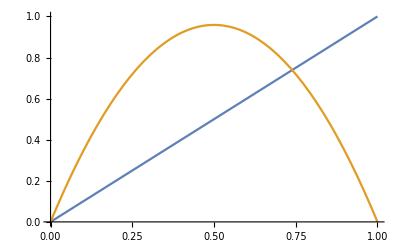

```mathematica
Plot[{x,f3[x]},{x,0,1}]
```

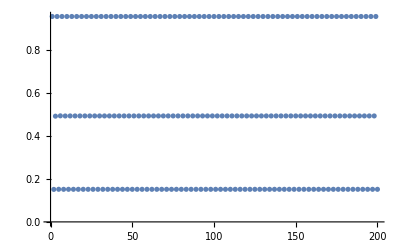

```mathematica
ListPlot[fn3[0.5,#]&/@Range[200]]
```

```mathematica
{a,b,c}= fn3[0.5,#]&/@{50,51,52}
I0={a,b};
I1={b,c};
(*50 iterazioni sono per stabilizzare eventuali convergenze*)
```

{0.152074,0.494514,0.958635}

Vogliamo dimostrare l’esistenza di un punto fisso (n=1)

```mathematica
{f3[a]==b,f3[b]==c}
```

{True,True}

⇒[a,c] ⊆f3(I_1) ⇒ (Brower) ∃ un punto fisso nell’interno di I_1
in effetti sappiamo che (μ - 1)/μ ≈

```mathematica
(3.835-1)/3.835
```

0.739244

è punto fisso (sempre) ed è interno a [b,c]

sia ora n>1, n≠3, vogliamo dimostrare l’esistenza di un’orbita di periodo n
per fare questo costruiamo J_n⊂...⊂ J_2⊂J_1⊂J_0=I_1
f(J_k)= J_(k-1) ∀k = 1 ... n-2
f^k(J_k)= I_1
f^(n-1)(J_(n-1))= I_0
f^n(J_n)= I_1

Possiamo illustrare questo esempio cercando l’orbita di periodo 5 (la successiva a 3 nell’ordine di Sharkovskiy)

```mathematica
{α,β,γ,δ,ϵ}=Flatten[{α,β,γ,δ,ϵ}/.FindInstance[{f3[α]==β,f3[β]==γ,f3[γ]==δ,f3[δ]==ϵ,f3[ϵ]==α,α≠0,β≠0,γ≠0,δ≠0,ϵ≠0},{α,β,γ,δ,ϵ},Reals]]
```

{0.65095,0.871366,0.429855,0.939881,0.216697}

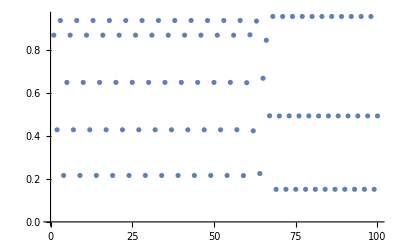

```mathematica
ListPlot[fn3[α,#]&/@Range[100]]
```

(imbrogliamo un po’) costruendo gli intervalli come da sopra

```mathematica
J={#-0.05,#+0.05}&/@{α,β,γ,δ,ϵ}
```

{{0.60095,0.70095},{0.821366,0.921366},{0.379855,0.479855},{0.889881,0.989881},{0.166697,0.266697}}

```mathematica
fJ=f3[#]&/@J
```

```mathematica
{{0.919667764206469,0.8038889906740951},{0.5626864357533385,0.2778488077566417},{0.903392573567774,0.9571936951816938},{0.3758035037219254,0.038415057148484234},{0.5327158763695897,0.7500094457487255}}
```

```mathematica
aaaaaa[q_]:= 
Module[{},J={#-q,#+q}&/@{α,β,γ,δ,ϵ};
fJ = RotateRight[f3[#] & /@ J];
Show[ListPlot[{{#,J⟦#,1⟧},{#,J⟦#,2⟧}}&/@Range[5], PlotStyle->Green],ListPlot[{{#,fJ⟦#,1⟧},{#,fJ⟦#,2⟧}}&/@Range[5], PlotStyle->Red]]]
```

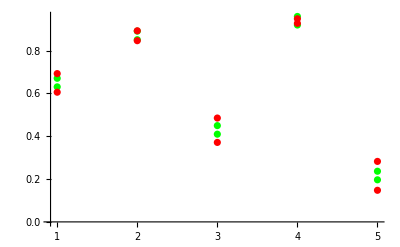

```mathematica
Manipulate[aaaaaa[q],{q,0,0.01}]
```

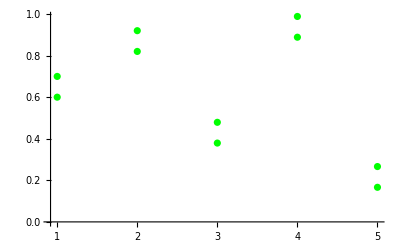

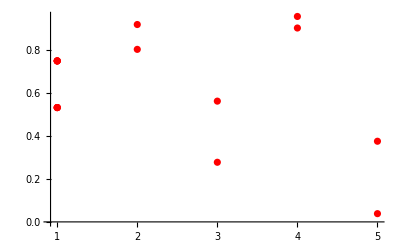

```mathematica
ListPlot[{{#,J⟦#,1⟧},{#,J⟦#,2⟧}}&/@Range[5], PlotStyle->Green]
```

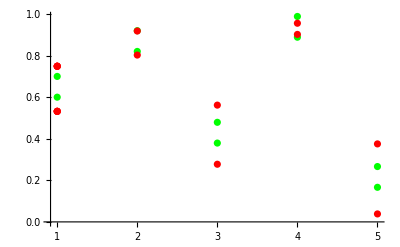

```mathematica
Show[%67,%68]
```

```mathematica
Clear[J]
```

{0.64095,0.79095}

{0.88256,0.63411}

{0.397489,0.889776}

{0.91845,0.376116}

{0.287241,0.899893}

{0.785153,0.345477}

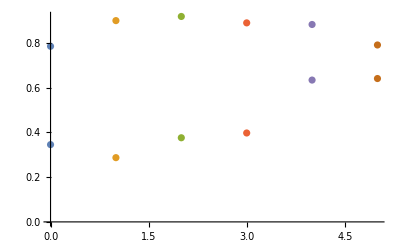

```mathematica
J[5]={α-0.01,α+0.14}
J[4]=f3[J[5]]
J[3]=f3[J[4]]
J[2]=f3[J[3]]
J[1]=f3[J[2]]
J[0]=f3[J[1]]
ListPlot[{{#,J[#]⟦1⟧},{#,J[#]⟦2⟧}}&/@Range[0,5]](*I don't fucking know what I'm doing*)
```

∃ p∈J_5 che è punto di orbita 5, in quanto è punto fisso per la quinta iterata di f (di nuovo per Brouwer).
p≠c poiché f(p)=f(c)=a e, dato che solo f^4permette di uscire da I_1 si avrebbe che n=2, indi c farebbe parte dell’orbita 2-periodica.
p≠b poiché f^2(p)=f^2(b)=a porterebbe ad avere che p fa parte dell’orbita 3-periodica, ma abbiamo deciso a priori di escludere n=3
quindi p∈(b,c) = ma f^4(p)∈I_0 ⇒ p≠f^4(p) (appartengono ad intervalli disgiunti) quindi p appartiene ad un’orbita di periodo minimo strettamente maggiore di n-1, quindi di periodo n

si vede facilmente che questa dimostrazione non usa l’ordine di Sharkovskiy, (in effetti dimostra solo che avere un orbita di periodo 3 implica avere orbite di ogni periodo)
la dimostrazione completa del teorema di Sharkovskiy è più complessa e non ho esattamente voglia di studiarla al momento, tuttavia rimane interessante guardare una delle sue implicazioni nella nostra mappa preferita

Grazie alla costruzione degli intervalli dovremmo trovare in J_5 il punto che possiede un’orbita di periodo 5. vediamo

#### The Full Proof

la Dimostrazione del teorema di Sharkovskiy si può ricavare dai seguenti tre punti:
·(a)· Se f ha un punto che genera una n-orbita per n>2, allora possiede una 2-orbita
·(b)· Se f ha un punto che genera un’orbita di periodo dispari m≥3 allora f possiede una n-orbita per ogni n≥m+1
·(c)·  Se f ha un punto che genera un’orbita di periodo dispari m≥3 allora f possiede una n-orbita per ogni n pari.

### Dimostriamo a)

usufruiremo dei seguenti Lemmi:
Lemma 1- siano k,m,n,s ∈ ℕ
i) se y genera una m-orbita di f, allora è un punto periodico di f^n di periodo m/(GCD(m,n)) 
ii) se y è punto periodico di f^n di periodo k allora è punto periodico di periodo kn/sove s|n, s e k coprimi
dim - 
la dimostrazione è banale se consideriamo che {f^k(y):k≤n}≃C_n visto come gruppo secondo la composizione di funzioni (cristo quanto mi sento il pisello lungo ad usare l’algebra per studiare i punti orbitali delle funzioni)

Lemma 2- siano c,d∈I t.c. f(d)≤c<d≤f(c) allora f ha un punto periodico di periodo 2
dim- 
sia I=[a,b], w = min_(c ≤ x ≤  d) (f(x)=x) e v: f(v)=d, indi f^2(v)=f(d) ≤ c ≤ d
Se f non ha punti fissi in [a,c] allora non ne ha in [a,v]. Visto che f^2(a)≥a allora f ha un punto 2-periodico in [a,v].
Se f invece ha un punto fisso in [a,c] allora sia t=max_(a ≤ x < c)(f(x)=x), in questo modo f non ha punti fissi in (t,v] . Sia ora u un punto in [t,c] con f(u)=c, si ha che f^2(u) = f(c) ≥ d ≥ u 
abbiamo quindi che f^2(u)≥ u, f^2(v)≤v possiamo quindi concludere (per Weierstrass) che ∃ y ∈ [u,v] t.c. f^2(y)=y 
dal momento che f non ha punti fissi in [u,v] allora y è punto 2-periodico per f.

#### Dim-

Sia P={x_i:i=1...m} una m-orbita di f, ove x_i< x_j ⇔ i<j
x_1<f(x_1) e f(x_m)< x_m ⇒ ∃s∈ℕ t.c. 1 ≤ s ≤ m-1 e x_s = max_(x∈P) (x<f(x)) 
ergo f(x_(s+1)) ≤ x_s <  x_(s+1) ≤  f(x_s)
si conclude dal Lemma 2

### Dimostriamo b e c)

I punti b) e c) si dimostrano facendo vedere che se esiste un ciclo di intervalli J_0... J_n t.c. J_(i+1) ⊂ f(J_i) e f(J_n)= J_0
se f ha una n-orbita per n≥3 allora ha un’orbita per ogni m>n+1 e di ogni periodo pari
lo si può fare generalizzando la dimostrazione illustrata:
sia x_1 un punto di periodo n>3 quindi t.c. f: x_1 ↦ x_2 ↦... ↦ x_n↦ x_1

∃ p∈J_n che è punto di orbita n, in quanto è punto fisso per la n-esima iterata di f (di nuovo per Brouwer).
p≠x_(n-1) poiché f(p)=f(x_(n-1)) = x_1 e, dato che solo f^(n-1)permette di uscire da I_1 si avrebbe che n=2, indi c farebbe parte dell’orbita 2-periodica.
.
.
.
p≠x_2 poiché f^(n-1)(p)=f^(n-1)(x_2)=x_1 porterebbe ad avere che p fa parte dell’orbita (n-1)-periodica, ma abbiamo deciso a priori di escludere m≤n

eccetera;

### Conclusiva:

da b) e c) possiamo concludere 3→5→7→...2*3→2*5→...
Se f ha punti 2m-periodici allora f^2 ha punti di periodo m ⇒^(b) f^2ha punti (m+2)-periodici ⇒^(L1.2)f ha punti (m+2)-periodici o 2(m+2)-periodici ⇒^(b) in ogni caso f ha punti 2(m+2)-periodici 
d’altro canto ⇒^(c) f^2 ha punti 6-periodici ⇒^(L1.2)f ha punti (2^2·3)-periodici
Ora, se f ha punti (2^km)-periodici per m dispari ≥3 per k≥2 allora ⇒^(L1.1)f^(2^(k-1)) ha punti 2(m+2)-periodici
quindi ripetendo il ragionamento f^(2^(k-1))ha punti 2(m+2) e 2^2·3 - periodici
quindi f ha punti di periodo 2^k(m+2) e 2^(k+1)
dal momento che f ha punti di periodo 2^km allora f^(2^k)ha punti di periodo m
⇒^(b) f ha punti di periodo 2^n>m ⇒^(L1.2) f ha punti (2^(k+n)) per ogni n t.c. 2^(n>m)

in fine se f ha punti di periodo 2^i (i≥2) allora f^(i-2) ha punti di periodo 4 ⇒^(a) f^(2^(i-2)) ha punti 2-periodici ⇒ f ha punti 2^(i-1)-periodici.
questo conclude la dimostrazione inducendo l’ordine di Sharkovskiy sui punti orbitali.

## Ciò che aggiunse il Pirla

```mathematica
f[μ_,x_]:=μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
fnList[μ_,x_,n_]:=NestList[RootReduce[f[μ,#]]&,x,n]
f3:=f[3835/1000,#]&
```

```mathematica
α=First@Flatten[α/.FindInstance[{f3[α]==β,f3[β]==γ,f3[γ]==δ,f3[δ]==ε,f3[ε]==α,α≠0,β≠0,γ≠0,δ≠0,ε≠0},{α,β,γ,δ,ε},Reals]];
```

```mathematica
orbita5=fnList[3835/1000,α,150];
```

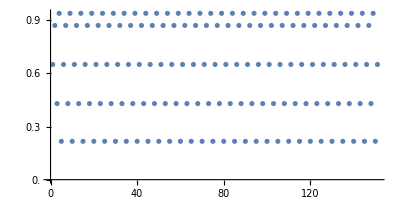

```mathematica
ListPlot[orbita5,AspectRatio->1/2,Ticks->{Range[0,150,10],Range[0,1,0.1]},ImageSize->Scaled[0.75]]
```